# Метод на разполовяването

x^3 - (b + 40)sinx - 3(a+b+1) = 0 (a=6, b=7)

```mathematica
f[x_]:=  x^3 - 47Sin[x] - 42
```

```mathematica
f[x]
```

-42+x^3-47 Sin[x]

## 1. Визуализация на функцията

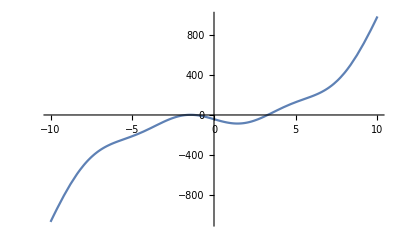

```mathematica
Plot[f[x],{x,-10,10}]
```

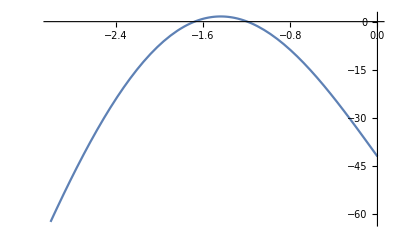

```mathematica
Plot[f[x],{x,-3,0}]
```

Брой корени: 3

## 2. Да се локализира най-големия корен.

Локализираме най-големия корен

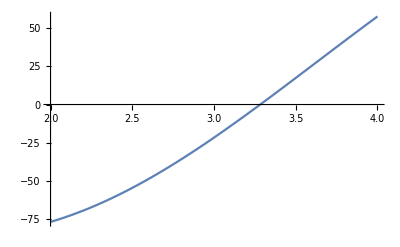

```mathematica
Plot[f[x],{x,2,4}]
```

```mathematica
f[2.]
```

-76.737

```mathematica
f[4.]
```

57.5697

Извод:
(1) Функцията е непрекъсната, защото е сума от непрекъснати функции (полином и синус)
(2) f(2) = -76.737... < 0
       f(4) = 57.5697... > 0
       => Функцията има различни знаци в двата края на разглеждания интервал [2; 4].
       От (1) и (2) следва, че функцията има поне един корен в разглеждания интервал [2; 4].

## 3. Уточнете локализирания корен по метода на разполовяването с 6 итерации.

```mathematica
f[x_]:=  x^3 - 47Sin[x] - 42
a =  2.;b = 4.;
For[n = 0, n <=3 , n++, 
Print["n = ",n, " a_n = ",a, " b_n = ",b, " m_n = ",m =  (a + b)/2  ,  " f(m_n) = ",f[m], " ε_n = ", (b - a)/2];
If[f[m] > 0, b = m, a = m]
]
```

n = 0 a_n = 2. b_n = 4. m_n = 3. f(m_n) = -21.6326 ε_n = 1.

n = 1 a_n = 3. b_n = 4. m_n = 3.5 f(m_n) = 17.3618 ε_n = 0.5

n = 2 a_n = 3. b_n = 3.5 m_n = 3.25 f(m_n) = -2.5867 ε_n = 0.25

n = 3 a_n = 3.25 b_n = 3.5 m_n = 3.375 f(m_n) = 7.31417 ε_n = 0.125

Извод: На третата итерация сме получили приближено решение 3.375 с точност 0.125

## 4. Оценка на грешката с точност ε = 10^-10

Цикъл при достигане на определена предварително зададена точност (със стоп-критерий):

```mathematica
f[x_]:=  x^3 - 47Sin[x] - 42
a =  2.;b = 4.;
epszad = 0.0000000001;
eps =  Infinity;
For[n = 0, eps > epszad , n++, 
Print["n = ",n, " a_n = ",a, " b_n = ",b, " m_n = ",m =  (a + b)/2  ,  " f(m_n) = ",f[m], " ε_n = ", eps = (b - a)/2];
If[f[m] > 0, b = m, a = m]
]
```

n = 0 a_n = 2. b_n = 4. m_n = 3. f(m_n) = -21.6326 ε_n = 1.

n = 1 a_n = 3. b_n = 4. m_n = 3.5 f(m_n) = 17.3618 ε_n = 0.5

n = 2 a_n = 3. b_n = 3.5 m_n = 3.25 f(m_n) = -2.5867 ε_n = 0.25

n = 3 a_n = 3.25 b_n = 3.5 m_n = 3.375 f(m_n) = 7.31417 ε_n = 0.125

n = 4 a_n = 3.25 b_n = 3.375 m_n = 3.3125 f(m_n) = 2.34052 ε_n = 0.0625

n = 5 a_n = 3.25 b_n = 3.3125 m_n = 3.28125 f(m_n) = -0.12951 ε_n = 0.03125

n = 6 a_n = 3.28125 b_n = 3.3125 m_n = 3.29688 f(m_n) = 1.10398 ε_n = 0.015625

n = 7 a_n = 3.28125 b_n = 3.29688 m_n = 3.28906 f(m_n) = 0.486843 ε_n = 0.0078125

n = 8 a_n = 3.28125 b_n = 3.28906 m_n = 3.28516 f(m_n) = 0.178567 ε_n = 0.00390625

n = 9 a_n = 3.28125 b_n = 3.28516 m_n = 3.2832 f(m_n) = 0.0245039 ε_n = 0.00195313

n = 10 a_n = 3.28125 b_n = 3.2832 m_n = 3.28223 f(m_n) = -0.0525092 ε_n = 0.000976563

n = 11 a_n = 3.28223 b_n = 3.2832 m_n = 3.28271 f(m_n) = -0.0140042 ε_n = 0.000488281

n = 12 a_n = 3.28271 b_n = 3.2832 m_n = 3.28296 f(m_n) = 0.00524948 ε_n = 0.000244141

n = 13 a_n = 3.28271 b_n = 3.28296 m_n = 3.28284 f(m_n) = -0.00437745 ε_n = 0.00012207

n = 14 a_n = 3.28284 b_n = 3.28296 m_n = 3.2829 f(m_n) = 0.000435993 ε_n = 0.0000610352

n = 15 a_n = 3.28284 b_n = 3.2829 m_n = 3.28287 f(m_n) = -0.00197073 ε_n = 0.0000305176

n = 16 a_n = 3.28287 b_n = 3.2829 m_n = 3.28288 f(m_n) = -0.000767372 ε_n = 0.0000152588

n = 17 a_n = 3.28288 b_n = 3.2829 m_n = 3.28289 f(m_n) = -0.00016569 ε_n = 7.62939×10^-6

n = 18 a_n = 3.28289 b_n = 3.2829 m_n = 3.28289 f(m_n) = 0.000135151 ε_n = 3.8147×10^-6

n = 19 a_n = 3.28289 b_n = 3.28289 m_n = 3.28289 f(m_n) = -0.0000152692 ε_n = 1.90735×10^-6

n = 20 a_n = 3.28289 b_n = 3.28289 m_n = 3.28289 f(m_n) = 0.0000599411 ε_n = 9.53674×10^-7

n = 21 a_n = 3.28289 b_n = 3.28289 m_n = 3.28289 f(m_n) = 0.000022336 ε_n = 4.76837×10^-7

n = 22 a_n = 3.28289 b_n = 3.28289 m_n = 3.28289 f(m_n) = 3.5334×10^-6 ε_n = 2.38419×10^-7

n = 23 a_n = 3.28289 b_n = 3.28289 m_n = 3.28289 f(m_n) = -5.86789×10^-6 ε_n = 1.19209×10^-7

n = 24 a_n = 3.28289 b_n = 3.28289 m_n = 3.28289 f(m_n) = -1.16724×10^-6 ε_n = 5.96046×10^-8

n = 25 a_n = 3.28289 b_n = 3.28289 m_n = 3.28289 f(m_n) = 1.18308×10^-6 ε_n = 2.98023×10^-8

n = 26 a_n = 3.28289 b_n = 3.28289 m_n = 3.28289 f(m_n) = 7.9171×10^-9 ε_n = 1.49012×10^-8

n = 27 a_n = 3.28289 b_n = 3.28289 m_n = 3.28289 f(m_n) = -5.79664×10^-7 ε_n = 7.45058×10^-9

n = 28 a_n = 3.28289 b_n = 3.28289 m_n = 3.28289 f(m_n) = -2.85873×10^-7 ε_n = 3.72529×10^-9

n = 29 a_n = 3.28289 b_n = 3.28289 m_n = 3.28289 f(m_n) = -1.38978×10^-7 ε_n = 1.86265×10^-9

n = 30 a_n = 3.28289 b_n = 3.28289 m_n = 3.28289 f(m_n) = -6.55305×10^-8 ε_n = 9.31323×10^-10

n = 31 a_n = 3.28289 b_n = 3.28289 m_n = 3.28289 f(m_n) = -2.88067×10^-8 ε_n = 4.65661×10^-10

n = 32 a_n = 3.28289 b_n = 3.28289 m_n = 3.28289 f(m_n) = -1.04448×10^-8 ε_n = 2.32831×10^-10

n = 33 a_n = 3.28289 b_n = 3.28289 m_n = 3.28289 f(m_n) = -1.26385×10^-9 ε_n = 1.16415×10^-10

n = 34 a_n = 3.28289 b_n = 3.28289 m_n = 3.28289 f(m_n) = 3.32663×10^-9 ε_n = 5.82077×10^-11

### Проверка

```mathematica
Log2[(4- 2)/0.0000000001] - 1
```

33.2193

Извод: Необходими са 34 итерации за достигане на исканата точност